# Задача 1

```mathematica
f[x_]=(-45(6+2)Cos[x]+x^3+23)/(6-x^2)
```

(23+x^3-360 Cos[x])/(6-x^2)

## Представете геометрична интерпретация на уравнението .

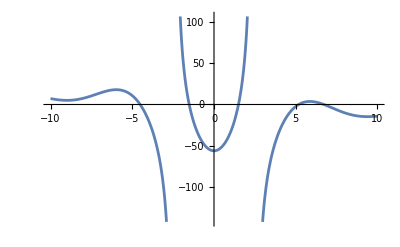

```mathematica
Plot[f[x], {x, -10, 10}]
```

```mathematica
Колко реални корена има?
```

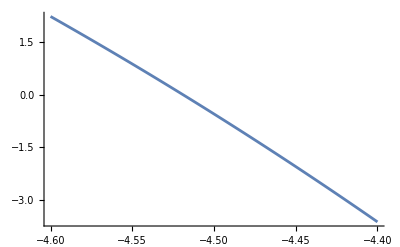

```mathematica
Plot[f[x], {x, -4.6, -4.4}]
(*първи корен*)
```

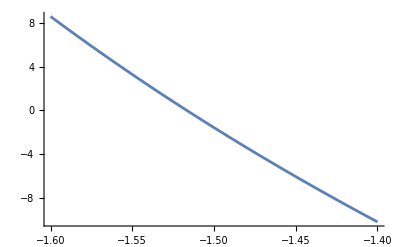

```mathematica
Plot[f[x], {x, -1.6, -1.4}]
(*втори корен*)
```

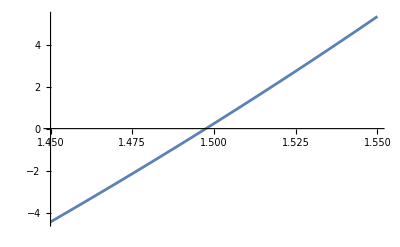

```mathematica
Plot[f[x], {x, 1.45, 1.55}]
(*трети корен*)
```

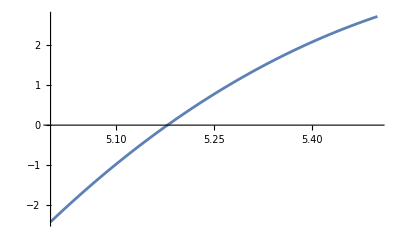

```mathematica
Plot[f[x], {x, 5., 5.5}]
(*четвърти корен*)
```

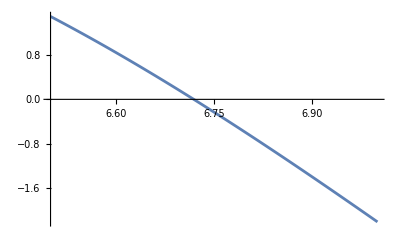

```mathematica
Plot[f[x], {x, 6.5, 7}]
(*пети корен*)
```

## Локализирайте корен (най - малкия) на уравнението .

```mathematica
Plot[f[x], {x, -4.6, -4.4}]
(*първи най-малък корен*)
```

-Graphics-

```mathematica
f[-4.6]
```

2.24018

```mathematica
f[-4.4]
```

-3.62693

Извод : (1) Функцията f (x) е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f (-4.6) = 2.24018 >0
f(-4.4) = -3.62693< 0
Функцията има различни знаци в двата края на разглеждания интервал[-4.6; -4.4] . Следователно от (1) и (2) следва, че в интервала[-4.6; -4.4] функцията има поне един
корен .